metodo de secante

```mathematica
f[x_] := x^x ⅇ^-x √(2π x)-120;
```

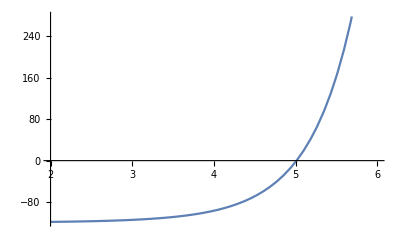

```mathematica
Plot[{F[x]},{x,2,6},PlotLegends->"Expressions"]
```

```mathematica
x[0] =4.6;
```

```mathematica
x[1]=5.3;
```

```mathematica
x[n_]:= (x[n-2]f[x[n-1]]-x[n-1]f[x[n-2]])/(f[x[n-1]]-f[x[n-2]]);
```

```mathematica
e[n_]:=Abs[x[n]-x[n-1]]/Abs[x[n]];
```

```mathematica
m = Table[{n,x[n-2],x[n-1],x[n],e[n],TrueQ[e[n]<10^-6]},{n,2,8}];
```

```mathematica
Insert[
Grid[Prepend[m,{"n","a_n","b_n","x_n","e_n","e_n<10^-6"}],Frame->All],Alignment->Left,2]
```

n | a_n | b_n | x_n | e_n | e_n<10^-6
2 | 4.6 | 5.3 | 4.90159 | 0.0812827 | False
3 | 5.3 | 4.90159 | 4.98288 | 0.0163153 | False
4 | 4.90159 | 4.98288 | 5.01247 | 0.00590226 | False
5 | 4.98288 | 5.01247 | 5.00966 | 0.000559561 | False
6 | 5.01247 | 5.00966 | 5.00973 | 0.0000133706 | False
7 | 5.00966 | 5.00973 | 5.00973 | 3.3281×10^-8 | True
8 | 5.00973 | 5.00973 | 5.00973 | 2.02945×10^-12 | True